```mathematica
Animate[Plot[Sin[2 x-p],{x,0,10}],{p,0,3},AnimationRunning->True]
```

```mathematica
Animate[Plot[Sin[x-a],{x,0,10}],{a,0,2 Pi},AnimationRunning->False]
```

```mathematica
Animate[Plot[Cos[p x]Cos[q x],{x,0,10},PlotRange->2],{p,1,5},{q,1,5},AnimationRunning->False]
```

```mathematica
cycloid[]:=Animate[Show[Plot[0,{x,-2,4 Pi+2},PlotStyle->Black],ParametricPlot[{t-Sin[t],1-Cos[t]},{t,-3,k}],Graphics[{Circle[{k,1},1],{Gray,Table[Line[{{k,1},{k+Cos[s],1+Sin[s]}}],{s,Pi/12,2 Pi,Pi/12}]},{PointSize[0.015],Red,Point[{k-Sin[k],1-Cos[k]}]}}],Ticks->None,Axes->False,AspectRatio->Automatic,PlotRange->{{-1,13.5},{0,2.1}},ImageSize->500],{k,-2,4 Pi+2},AnimationRunning->False]
cycloid[]
```

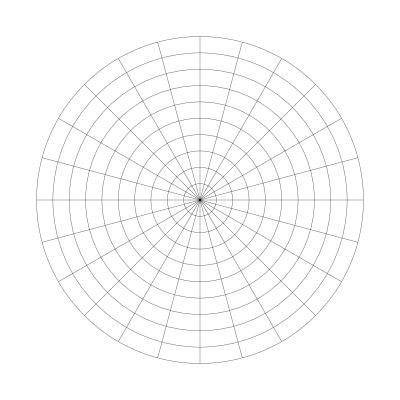

```mathematica
polarGrid[r_,dr_]:=Graphics[{Thickness[0.0005],Table[Circle[{0,0},k],{k,dr,r,dr}],Table[Line[{{0,0},r {Cos[t],Sin[t]}}],{t,Pi/12,2 Pi,Pi/12}]}]
polarGrid[1,.1]
```

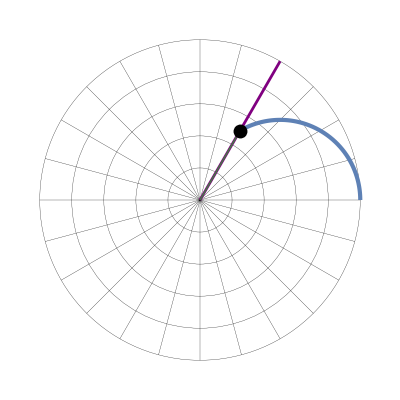

```mathematica
polarGrid[r_,dr_]:=Graphics[{Thickness[0.0005],Table[Circle[{0,0},k],{k,dr,r,dr}],Table[Line[{{0,0},r {Cos[t],Sin[t]}}],{t,Pi/12,2 Pi,Pi/12}]}]
polarCurve[r_,{t_,t1_,t2_},rmax_,opts___]:=Module[{r2=r/.t->t2,pt2={Cos[t2],Sin[t2]}},Show[polarGrid[rmax,rmax/5],PolarPlot[r,{t,t1,t2},PlotStyle->AbsoluteThickness[3]],Graphics[{{Purple,Thickness[.005],Line[{{0,0},rmax pt2}]},{If[r2>0,Green,Red],Thick,Opacity[.5],Line[{{0,0},r2 pt2}]},{PointSize[.025],Point[r2 pt2]}}],opts,PlotRange->1.02 rmax{{-1,1},{-1,1}}]]
polarCurve[Cos[t],{t,0,Pi/3},1]
```

```mathematica
polarMovie[r_,{t_,t1_,t2_},rmax_]:=Animate[GraphicsRow[{polarCurve[r,{t,t1,k},rmax],Plot[r,{t,t1,k},Ticks->{{Pi,2 Pi},None},PlotRange->{{t1,t2},{-rmax,rmax}},ImageSize->250]},20],{k,t1+Pi/12,t2,Pi/12},AnimationRunning->False]
```

```mathematica
polarMovie[Cos[2 t],{t,0,2 Pi},1]
```

```mathematica
polarMovie[Sin[4 t],{t,0,2 Pi},1]
```

```mathematica
polarMovie[2 (1-Cos[t])/5,{t,0,2 Pi},1]
```

```mathematica
Manipulate[Factor[x^n-1],{n,2,20,1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,6}],{a,1,4,Appearance->"Labeled"},{b,0,10,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[a x^2+b x+c,{x,-10,10},PlotRange->{-50,50},PlotLabel->Row[{y==a x^2+b x+c}]],{{a,3},-10,10,Appearance->"Labeled"},{{b,-5},-10,10,Appearance->"Labeled"},{{c,-9},-10,10,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Module[{d=b^2-4 a c,r},If[d≥0,r={{(-b-√d)/(2 a),0},{(-b+√d)/(2 a),0}},r={{-1000,0},{1000,0}}];
Plot[a x^2+b x+c,{x,-10,10},PlotRange->{-50,50},
PlotLabel->
Row[{y==a x^2+b x+c,"\n D=",b^2-4 a c,Which[d<0,",   No Roots \n",d==0,"=0,   Duplicate Root \n",
d>0,">0,   Two Roots \n"]}],Epilog->{Red,PointSize[0.015],Point[r]}]],
{{a,3},-10,10,Appearance->"Labeled"},{{b,-5},-10,10,Appearance->"Labeled"},{{c,-9},-10,10,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[a x^3+b x^2+c x+d,{x,-10,10},PlotRange->{-50,50},PlotLabel->Row[{y==a x^3+b x^2+c x+d}]],{{a,0.5},-10,10,Appearance->"Labeled"},{{b,-2},-10,10,Appearance->"Labeled"},{{c,-9},-10,10,Appearance->"Labeled"},{{d,9},-10,10,Appearance->"Labeled"}]
```

4.2 x^2+0.5 x-0.5

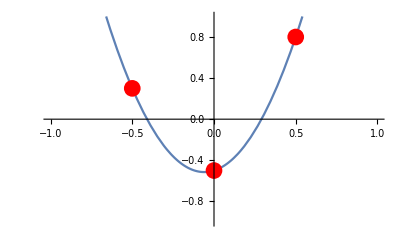

```mathematica
pt1={-0.5,0.3};
pt2={0,-0.5};
pt3={0.5,0.8};
TraditionalForm[Expand[InterpolatingPolynomial[{pt1,pt2,pt3},x]]]
Plot[InterpolatingPolynomial[{pt1,pt2,pt3},x],{x,-1,1},Epilog->{PointSize[0.03],Red,Point[{pt1,pt2,pt3}]},PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
pts={{-0.5,0.3},{0,-0.5},{0.5,0.8}};
TraditionalForm[Expand[InterpolatingPolynomial[pts,x]]]
Plot[InterpolatingPolynomial[pts,x],{x,-1,1},Epilog->{PointSize[0.03],Red,Point[pts]},PlotRange->{{-1,1},{-1,1}}]
```

4.2 x^2+0.5 x-0.5

-Graphics-

```mathematica
Manipulate[Plot[InterpolatingPolynomial[{pt1,pt2,pt3},x],{x,-1,1},PlotRange->{{-1,1},{-1,1}}],{{pt1,{-0.5,0.3}},Locator},{{pt2,{0,-0.5}},Locator},{{pt3,{0.5,0.8}},Locator}]
```

```mathematica
Manipulate[Plot[InterpolatingPolynomial[pts,x],{x,-1,1},PlotRange->{{-1,1},{-1,1}}],{{pts,{{-0.5,0.3},{0,-0.5},{0.5,0.8}}},Locator}]
```

```mathematica
Manipulate[Plot[InterpolatingPolynomial[pts,x],{x,-3,3},PlotRange->All],{{pts,{{-2.5,0},{-1,2},{1,-2},{3,1}}},Locator}]
```

```mathematica
Manipulate[Plot[InterpolatingPolynomial[pts,x],{x,-3,3},PlotRange->{{-3,3},{-3,3}}],{{pts,{{-2.5,0},{-1,2},{1,-2},{3,1}}},Locator}]
```

```mathematica
f[x_]:=2 (x-1) (x-1.5) (x-.5) (x+1) (x+1.5);
g[x_]:=0.4 x-0.4;
Solve[f[x]==g[x],x]
Manipulate[Plot[Evaluate[{f[x],g[x]}],{x,-1.5,1.52},Epilog->{Red,PointSize[Large],Point[{#,f[#]}&/@ (x/.Solve[f[x]==g[x],x])]}],{a,-0.8,.5,.2}]
```

{{x→-1.55709},{x→-0.900753},{x→0.432319},{x→1.},{x→1.52552}}

```mathematica
p1=ContourPlot[Sin[x y],{x,-3 π,3 π},{y,-3 π,3 π},ContourShading->False];
Manipulate[Show[p1,Graphics[{Red,AbsolutePointSize[5],Dynamic@Point[pt1]}],PlotRange->{{-3 π,3 π},{-3 π,3 π}}],{{pt1,{0,0}},{-3 π,3 π},{3 π,3 π},Locator}]
```

```mathematica
Manipulate[Graphics[{BezierCurve[pts,SplineDegree->d],Dashed,Green,Line[pts]},PlotRange->5,Frame->True],{{pts,{{-3,0},{-1,3},{1,-3},{3,0}}},Locator,LocatorAutoCreate->True},{{d,3,"degree"},2,6,1}]
```

```mathematica
Manipulate[Graphics[{BezierCurve[pts,SplineDegree->3],Dashed,Blue,Line[pts]},PlotRange->5,Frame->True],{{pts,{{-3,0},{-1,3},{1,-3}}},Locator}]
```

```mathematica
Manipulate[Graphics[{BezierCurve[pts,SplineDegree->2],Dashed,Blue,Line[pts]},PlotRange->5,Frame->True],{{pts,{{-3,0},{-1,3},{1,-3},{3,0}}},Locator}]
```

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0},{4,-2},{5,1}};
Graphics[{Point[pts],BSplineCurve[pts,SplineWeights->Automatic]}]
```

-Graphics-

```mathematica
Graphics[{Point[pts],BSplineCurve[pts,SplineWeights->{1,1,10,1,1,1}]}]
```

-Graphics-

```mathematica
Manipulate[Graphics[Line[{{0,0},p}],PlotRange->2],{{p,{1,1}},Locator}]
Manipulate[Graphics[Map[Point[#]&,pts],PlotRange->1],{{pts,{{0,0},{.5,0},{0,.5}}},Locator,LocatorAutoCreate->True}]
```

```mathematica
Manipulate[Graphics[Map[Point[#]&,pts],PlotRange->1],{{pts,{{0,0},{.5,0},{0,.5}}},Locator,LocatorAutoCreate->True}]
```